```mathematica
cRaleigh2[α_,β_,ν_]:=Module[{answer,pchhmrA,pchhmrB},
pchhmrA=Pochhammer[α,ν];
pchhmrB=Pochhammer[β,ν];
answer=pchhmrA*pchhmrB/(ν!)^2;
Return[answer]]
```

```mathematica
eRaleigh[α_,β_,ν_]:=Sum[1/(α+p)+1/(β+p)-2/(1+p),{p,0,ν-1}]
```

```mathematica
Fraleigh2[α_,β_,u_,terms_]:=Sum[cRaleigh2[α,β,ν]*u^ν,{ν,0,terms}]
```

```mathematica
FstarRaleigh2[α_,β_,u_,terms_]:=
Module[{ν,fsr},
fsr=Sum[cRaleigh2[α,β,ν]*eRaleigh[α,β,ν]*u^ν,{ν,1,terms}];
Return[fsr]]
```

```mathematica
FstarRaleigh3[n_,m_,x_]:=
Module[{α,β,fsr2},
α = 1/2(1/2-1/m);
 β = 1/2(1/2+1/m);
fsr2=FstarRaleigh2[α,β,x,n];
fsr2=Series[fsr2,{x,0,n}];
Return[fsr2]]
```

```mathematica
Fraleigh4[n_,m_,x_]:=
Module[{α,β,fr2},
α = 1/2(1/2-1/m);
 β = 1/2(1/2+1/m);
fr2=Fraleigh2[α,β,x,n];
fr2=Series[fr2,{x,0,n}];
Return[fr2]]
```

```mathematica
exNo3[n_,m_,J_]:=
Module[{a1,a2,a3,a4},
a1=J*Exp[FstarRaleigh3[n,m,J]/Fraleigh4[n,m,J]];
a2=Series[a1,{J,0,n}];
a3=Collect[Normal[a2],J];
a4=Series[a3,{J,0,n}];
Return[a4]]
```

```mathematica
J[n_,m_]:=1/InverseSeries[exNo3[n,m,x],x]
```

```mathematica
jNew[n_,m_]:=
Module[{ns,collect1,cf,collect2},
ns=Normal[J[n,m]]/.x->(2^6*m^3*x);
collect1=Collect[ns,x];
cf=Coefficient[collect1,x,-1];
collect2=Collect[collect1/cf,x];
Return[collect2]]
```

```mathematica
fsubi2[n_,m_]:=
Module[{jay,numerator,denominator,answer,answer2},
jay=jNew[n+1,m];
numerator=x^m*D[jay,x]^m;
denominator=jNew[n+1,m]^(m-1)*(jNew[n+1,m]-2^6* m^3);
answer=Normal[Series[(numerator/denominator)^(1/(m-2)),{x,0,n}]];
answer=Refine[answer,x>0];

If[Mod[m,2]==1,answer=Collect[answer/(-1)^(1/(m-2)),x]];

Return[answer]]
```

```mathematica
leadingTermCoefficient[polynomial_]:=Module[{degree,leading},
degree=Exponent[polynomial,x];
leading=Coefficient[polynomial,x,degree];
Return[leading]]
```

```mathematica
rationalQ[x_]:=
IntegerQ[Numerator[x]]&&IntegerQ[Denominator[x]]&&!(Denominator[x]==0);
Attributes[rationalQ]=Listable
```

Listable

```mathematica
polyIsConstantQ[polynomial_]:=Module[{tf},
tf=False;
If[rationalQ[polynomial]==True,tf=True];
Return[tf]]
```

```mathematica
mckayThompson[n_]:=SeriesCoefficient[QPochhammer[-q,q^2]^24/q,{q,0,n}]
```

```mathematica
(* testing below code.... *)
fromPolyToNumberTimesMonic[polynomial_]:=
Module[{ltp},
ltp=leadingTermCoefficient[poly];
Return[{ltp,Collect[poly/ltp,x]}]];


monicPolynomialQ2[polynomial_,x_]:=
Module[{tf},
tf=True;
If[(PolynomialQ[polynomial,x]===False)||(leadingTermCoefficient[polynomial,x]!=1),tf==False];
Return[tf]];

baseConstantQ[pair_]:=
Module[{tf,bbase},
tf=False;
bbase=pair[[1]];
If[polyIsConstantQ[bbase]==True,tf=True];
Return[tf]
];
baseNotConstantQ[pair_]:=Not[baseConstantQ[pair]];

factorIntoMonics[polynomial_]:=
Module[{factor,factors,nonconstants,
lnf,lnt,lncf,monicfactor,monicfactorbase,monicfactors,numericalterm,k,kk,leadngterm,base,exponent,number,fpntm},
monicfactors={};
factors=FactorList[polynomial];

numericalterm=Select[factors,baseConstantQ];

lnt=Length[numericalterm];
number=Product[numericalterm[[kk,1]]^numericalterm[[kk,2]],{kk,1,lnt}];
nonconstants=Select[factors,baseNotConstantQ];
lncf=Length[nonconstants];
For[k=0,k<lncf,k++;
factor=nonconstants[[k]];
base=factor[[1]];
exponent=factor[[2]];
poly=base^exponent;
fpntm=fromPolyToNumberTimesMonic[poly];
number=number*fpntm[[1]];
AppendTo[monicfactors,fpntm[[2]]]];
Return[Flatten[{number,monicfactors}]]];

fromMonicFactorsToPolynomial[list_]:=
Module[{j,len,poly,base,exponent,pair},
poly=1;
len=Length[list];
For[j=0,j<len,j++;
poly=poly*list[[j]]];
Return[poly]]
```

```mathematica
oddQ[n_]:=Module[{tf},
tf=True;
If[Mod[n,2]===0,tf=False];
Return[tf]]
```

```mathematica
specialsum2[n_]:=Module[{},
If[n===0,Return[1]];
If[n!=0,Return[(-1)^n*24*Total[Select[Divisors[n],oddQ]]]]]
```

```mathematica
stream=OpenWrite["run6sept20no10"];
start=SessionTime[];
For[m=2,m<302,m++;
expansion=fsubi2[100,m];
Write[stream,{m,expansion}]];
Close[stream];
Print["elapsed seconds = ",SessionTime[]-start]
```

elapsed seconds = 255322.34512

```mathematica
stream=OpenRead["run6sept20no10"];
list=ReadList[stream];
Close[stream];
a=Length[list];
b=Last[list][[1]];
Print[{a,b}]
```

{300,302}

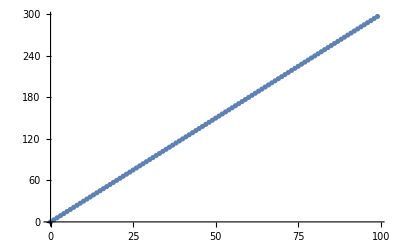

run14sept20no4

```mathematica
stream=OpenRead["run6sept20no10"];
list=ReadList[stream];
Close[stream];
wstream=OpenWrite["run14sept20no4"];
degrees={};
For[n=-1,n<99,n++;
data={};
For[k=0,k<300,k++;
m=list[[k,1]];
poly=list[[k,2]];
cf=Coefficient[poly,x,n];
AppendTo[data,{m,cf}]
]; (* k *)
ip=Collect[InterpolatingPolynomial[data,x],x];
ip=Expand[ip];
Write[wstream,{n,ip}];
AppendTo[degrees,{n,Exponent[ip,x]}]
]; (* n *)
Print[ListPlot[degrees]];
Close[wstream]
```

```mathematica
pstream=OpenRead["run14sept20no4"];
(* interpolating polynomials *)
plist=ReadList[pstream];
Close[pstream];
Print[Length[plist]]
```

100

#### Conjecture 3 clause 1(a)

```mathematica
stream=OpenRead["run14sept20no4"];
(* interpolating polynomials *)
list=ReadList[stream];
Close[stream];
xdata={};
For[k=0,k<100,k++;
n=list[[k,1]];
poly=list[[k,2]];
poly=Collect[poly,x];
dg=Exponent[poly,x];
AppendTo[xdata,{n,dg-3*n}]];
Print[xdata]
```

{{0,0},{1,0},{2,0},{3,0},{4,0},{5,0},{6,0},{7,0},{8,0},{9,0},{10,0},{11,0},{12,0},{13,0},{14,0},{15,0},{16,0},{17,0},{18,0},{19,0},{20,0},{21,0},{22,0},{23,0},{24,0},{25,0},{26,0},{27,0},{28,0},{29,0},{30,0},{31,0},{32,0},{33,0},{34,0},{35,0},{36,0},{37,0},{38,0},{39,0},{40,0},{41,0},{42,0},{43,0},{44,0},{45,0},{46,0},{47,0},{48,0},{49,0},{50,0},{51,0},{52,0},{53,0},{54,0},{55,0},{56,0},{57,0},{58,0},{59,0},{60,0},{61,0},{62,0},{63,0},{64,0},{65,0},{66,0},{67,0},{68,0},{69,0},{70,0},{71,0},{72,0},{73,0},{74,0},{75,0},{76,0},{77,0},{78,0},{79,0},{80,0},{81,0},{82,0},{83,0},{84,0},{85,0},{86,0},{87,0},{88,0},{89,0},{90,0},{91,0},{92,0},{93,0},{94,0},{95,0},{96,0},{97,0},{98,0},{99,0}}

#### Conjecture 3 clause 1(b)

#### From looking at OEIS A103640 and A004011.

```mathematica
stream=OpenRead["run14sept20no4"];
list=ReadList[stream];
Close[stream];
data={};
For[k=0,k<100,k++;
n=list[[k,1]];
poly=list[[k,2]];
poly=factorIntoMonics[poly];
num=poly[[1]];
AppendTo[data,num-specialsum2[n]]]
Print[data]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

#### Conjecture 3 clause 2

```mathematica
mstream=OpenRead["run6sept20no10"];
(* H6 series *)
mlist=ReadList[mstream];
Close[mstream];
Print["length: ",Length[mlist]];
pstream=OpenRead["run14sept20no4"];
(* interpolating polynomials *)
plist=ReadList[pstream];
Close[pstream];
no={};
n=1;
For[k=0,k<300,k++;
m=mlist[[k,1]];
poly=mlist[[k,2]];
poly=Normal[Series[poly,{x,0,99}]];
(* the H6 series are taken to order 100; above line
of code lops off the x^100 term *)
cf=Coefficient[poly,x,n];

For[j=0,j<100,j++;
index=plist[[j,1]];
If[n===index,
ppoly=plist[[j,2]]; 
vm=ppoly/.x->m;
If[vm≠cf,AppendTo[no,{m,index}]]
] (* If[n  *)
] (* For[j  *)
] (* For[k *)

Print["no"];
Print[no]
```

length: 300

no

{}

#### Conjecture 3 clause 3

```mathematica
stream=OpenRead["run14sept20no4"];
list=ReadList[stream];
Close[stream];
data={};
For[k=0,k<3,k++;
n=list[[k,1]];
poly=list[[k,2]];
poly=Collect[poly,x];
poly=factorIntoMonics[poly];
Print["============================================================"];
Print["n: ",n];
Print[poly]]
```

============================================================

n: 0

{1}

============================================================

n: 1

{-24,x^2,-2/3+x}

============================================================

n: 2

{24,-14+x,-2+x,x^3,-2/3+x}

```mathematica
stream=OpenRead["run14sept20no4"];
list=ReadList[stream];
Close[stream];
Print[Length[list]]
```

100

#### Conjecture 3 clause 4

```mathematica
stream=OpenRead["run14sept20no4"];
list=ReadList[stream];
Close[stream];
yes1=0;
no1=0;
yes2=0;
no2=0;
yes3=0;
no3=0;
yes4=0;
no4=0;
yes5=0;
no5=0;
diffs={};
For[j=0,j<100,j++;
Clear[poly];
n=list[[j,1]];
If[n>2,
poly0=list[[j,2]];
list2=factorIntoMonics[poly0];
last=Last[list2];

(* question 1 *)
If[monicPolynomialQ2[last,x]===True,yes1++];
If[monicPolynomialQ2[last,x]===False,
Print["++++++++++++++++++++++++++++++++++++++++++++++++++++++"];
Print["no for n = ",n];
Print["leading term coefficient ",leadingTermCoefficient[last]];
Print["is 'last' a polynomial:  ",PolynomialQ[last,x]];
no1++];

(* question 2 *)
If[IrreduciblePolynomialQ[last]===True,yes2++];
If[IrreduciblePolynomialQ[last]===False,no2++];

(*question3 *)
cl=CoefficientList[last,x];
If[AllTrue[cl,rationalQ],yes3++];
If[Not[AllTrue[cl,rationalQ]],no3++];

(*question 4*)
test=Collect[specialsum2[n]*(x-2)*(x-2/3)*x^(n+1)*last,x];
diff=test-poly0;
diffs=Append[diffs,diff];
If[poly0===test,yes4++];
If[poly0≠test,no4++];

(* question 5 *)
degree=Exponent[poly0,x];
If[degree===3*n,yes5++];
If[degree≠3*n,no5++];
deglast=Exponent[last,x];

] (* If[n>1 *)

];
Print["question 1: ",{yes1,no1}];
Print["question 2: ",{yes2,no2}];Print["question 3: ",{yes3,no3}];Print["question 4: ",{yes4,no4}];Print["question 5: ",{yes5,no5}]
```

question 1: {97,0}

question 2: {97,0}

question 3: {97,0}

question 4: {97,0}

question 5: {97,0}